```mathematica
(*#8 For the following functions, sketch the Fourier series of f(x) (on the interval −L < x <.14 L).Compare
f(x) to its Fourier series:*)
```

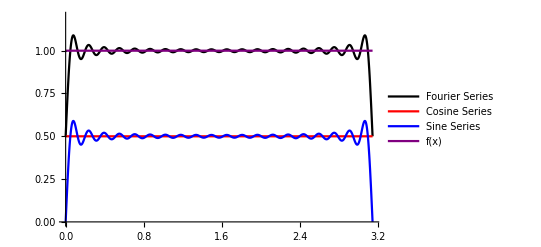

```mathematica
(*Problem #8 part a*)
(*Plot the Fourier,Cosine,Sine Series f[x] = 1 on the interval [-L,L]*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,0,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,0,L}]*(1/L)
f[x_]=1;
L=Pi;

a[n];
b[n];

Table[a[n],{n,0,10}];
Table[b[n],{n,0,10}];

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2

Plot[{Evaluate[myFourier[x,40]],Evaluate[myFCos[x,40]],Evaluate[myFSin[x,40]],f[x]},{x,0,L},PlotStyle->{Black,Red, Blue, Purple},PlotLegends->{"Fourier Series","Cosine Series","Sine Series","f(x)"},PlotRange->{0,1.2}]
(*Graph of part a f(x) = 1*)
```

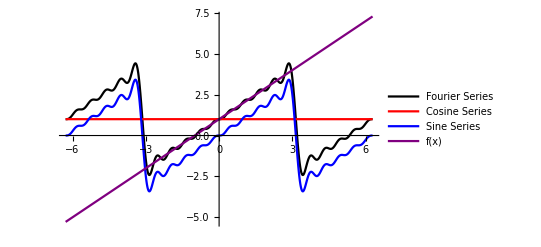

```mathematica
(*Problem #8 part b f(x) =1+x*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,-L,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,-L,L}]*(1/L)
f[x_]=1+x;
L=Pi;

a[n];
b[n];

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2

Plot[{Evaluate[myFourier[x,10]],Evaluate[myFCos[x,10]],Evaluate[myFSin[x,10]],f[x]},{x,-2L,2L},PlotStyle->{Black,Red, Blue, Purple},PlotLegends->{"Fourier Series","Cosine Series","Sine Series","f(x)"}]
```

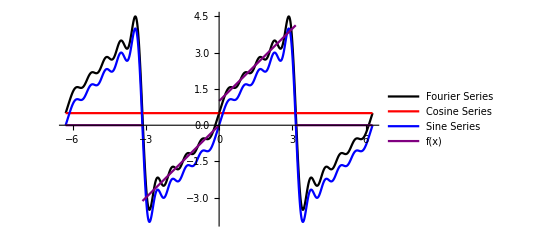

```mathematica
(*Problem #8 part c f(x) is a piecewise defined function*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,-L,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,-L,L}]*(1/L)
f[x_]:=Piecewise[{{x,x>=-L&&x<0},{1+x,x>0&&x<=L}}]
L=Pi;

a[n];
b[n];

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2


Plot[{Evaluate[myFourier[x,10]],Evaluate[myFCos[x,10]],Evaluate[myFSin[x,10]],f[x]},{x,-2L,2L},PlotStyle->{Black,Red, Blue, Purple},PlotLegends->{"Fourier Series","Cosine Series","Sine Series","f(x)"}]
(*Graph of part c f(x) = piecewise*)
(*Notice the change in the 'slopes' of the 'x' and 'x+1' part*)
```

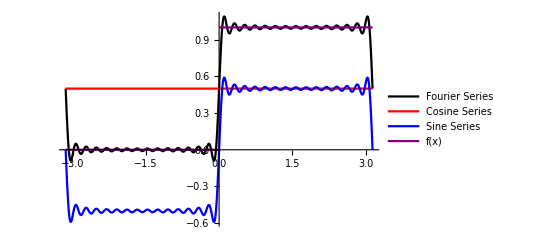

```mathematica
(*Problem #8 part d f(x) is a piecewise defined function*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,-L,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,-L,L}]*(1/L)
f[x_]:=Piecewise[{{0,x>=-L&&x<0},{1,x>0&&x<=L}}]
L=Pi;

a[n];
b[n];

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2


Plot[{Evaluate[myFourier[x,30]],Evaluate[myFCos[x,30]],Evaluate[myFSin[x,30]],f[x]},{x,-L,L},PlotStyle->{Black,Red, Blue, Purple},PlotLegends->{"Fourier Series","Cosine Series","Sine Series","f(x)"}]
(*Graph of part d piecewise*)
(*Notice that the graph switches form 0 and 1 at the origin*)
```